```mathematica
(*P50 HW2*)
(*Each question is worth 1 pt. You can type your answer directly below the questions. Please upload your solution in .nb or .pdf*)
```

```mathematica
(*Q1: For the series S = ∑_(n=0)^∞ 10 1.005^n, evaluate the n=120 term. And then perform sum up to n = 120. Do you think this series would converge? *)
```

```mathematica
Sum[10 1.005^n,{n,120,120}]
Sum[10 1.005^n,{n,0,120}]
(*Diverges since 1.005>1*)
```

18.194

1656.99

```mathematica
(*Q2: You are taking N-year-fixed loan (usually N= 10, 20 or 30) with zero downpayment to purchase a house. The fixed monthly payment is MP. And the APR of the loan is 12*r, i.e. the monthly rate is r). What is the purchase price P of the house? Ignor all fees.*)
```

```mathematica
(*hint: With zero downpayment,the principle of the loan is equal to the house price P. After the first month, the amount owed = P(1+r)- MP. After the 2nd month, the amount owed = (1+r) (P(1+r)- MP) - MP = P(1+r)^2 - (MP + MP(1+r)) ..... after the nth month, the amount owed = P(1+r)^n - ∑_(i=0)^(n-1) MP(1+r)^i. We know that the amount owed after n =12*N month is 0...*)
```

```mathematica
Solve[0 == P(1+r)^(12n) - Sum[MP(1+r)^i ,{i,0,12N-1}],P]
```

{{P→(MP (1+r)^(-12 n) (-1+(1+r)^(12 N)))/r}}

```mathematica
(*Q3: What is the Taylor expansion of ⅇ^x Sin[x] to the 4th order? Plot ⅇ^x Sin[x] and its Taylor expansion to the 4th order in the same plot for x between -2 and 2.*)
```

x+x^2+x^3/3+O[x]^5

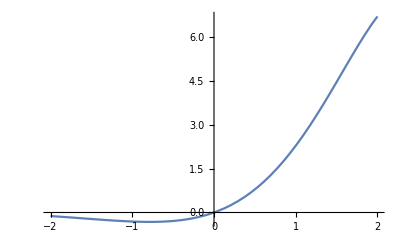

```mathematica
f3[x_]:=Exp[x]Sin[x]
Series[f3[x],{x,0,4}]
Plot[f3[x],{x,-2,2}]
```

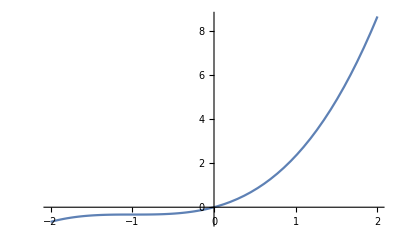

```mathematica
Plot[x+x^2+x^3/3,{x,-2,2}]
```

```mathematica
(*Q4: What is the Taylor expansion of Sin[x]/Sqrt[1-x^2] to the 5th order? What is the ingeral of that 5th order expansion for {x, 0, u} ? (the answer should be written down as a function of u)*)
```

```mathematica
f4[x_]:= Sin[x]/Sqrt[1-x^2]
texp= Series[f4[x],{x,0,5}]
Integrate[texp,{x,0,u}]
```

x+x^3/3+(3 x^5)/10+O[x]^6

1/60 u^2 (30+5 u^2+3 u^4)

```mathematica
(*Q5: Use the ratio test to tell if ∑_(n=1)^∞ 1/n^4 converges. Evaluate ∑_(n=1)^∞ 1/n^4 ,give both symboic (if possible) and numerical answers. *)
```

```mathematica
Limit[n^4/(n+1)^4,n -> Infinity]
```

1

```mathematica
ans = Sum[1/n^4,{n,1,Infinity}]
ans//N
```

π^4/90

1.08232

```mathematica
(*Q6: Use the ratio test to tell if ∑_(n=1)^∞ 1/n^n converges. Evaluate the series ,give both symboic (if possible) and numerical answers. *)
```

```mathematica
Limit[n^n/(n+1)^(n+1),n -> Infinity]
```

0

```mathematica
ans = Sum[1/n^n,{n,1,Infinity}]
ans//N
```

∑_(n=1)^∞ n^-n

1.29129

```mathematica
(*Q7: Write down the Taylor series of x^(1/3) about x0=8 and to the 3rd order*)
```

```mathematica
Series[x^(1/3),{x,8,3}]
```

2+(x-8)/12-1/288 (x-8)^2+(5 (x-8)^3)/20736+O[x-8]^4

```mathematica
(*Q8: Write down the Taylor series of Tan[x] about x0=0 and to the 5th order. Then write down its normal form without O[θ]^6.*)
```

```mathematica
Series[Tan[x],{x,0,5}]
%//Normal
```

x+x^3/3+(2 x^5)/15+O[x]^6

x+x^3/3+(2 x^5)/15

```mathematica
(*Q9: Solve {y''[x]-y[x]==0, y[0] = 1, y'[0]=0}using Taylor expasion to the 6th order.*)
```

```mathematica
f9[x_]:=Sum[a[n] x^n,{n,0,6}]/.{a[0]->1,a[1]->0}
f9''[x]-f9[x]==0
```

-1+2 a[2]-x^2 a[2]+6 x a[3]-x^3 a[3]+12 x^2 a[4]-x^4 a[4]+20 x^3 a[5]-x^5 a[5]+30 x^4 a[6]-x^6 a[6]==0

```mathematica
coeff=Table[Coefficient[f9''[x]-f9[x],x^n],{n,1,5}]
```

{6 a[3],-a[2]+12 a[4],-a[3]+20 a[5],-a[4]+30 a[6],-a[5]}

```mathematica
exptoeq[x_]:=x==0
eqs = Thread[exptoeq[coeff]]
```

{6 a[3]==0,-a[2]+12 a[4]==0,-a[3]+20 a[5]==0,-a[4]+30 a[6]==0,-a[5]==0}

```mathematica
eqs = Append[eqs,-1+2a[2]==0]
```

{6 a[3]==0,-a[2]+12 a[4]==0,-a[3]+20 a[5]==0,-a[4]+30 a[6]==0,-a[5]==0,-1+2 a[2]==0}

```mathematica
Solve[eqs,{a[2],a[3],a[4],a[5],a[6]}]
```

{{a[2]→1/2,a[3]→0,a[4]→1/24,a[5]→0,a[6]→1/720}}

```mathematica
%//Flatten
f9[x]/.%
```

{a[2]→1/2,a[3]→0,a[4]→1/24,a[5]→0,a[6]→1/720}

1+x^2/2+x^4/24+x^6/720